# Two Flavor Level Crossing

2.45272×10^-20 x

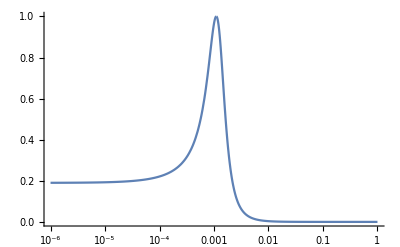

{{En→0.00110082}}

0.00110082

1.102/x

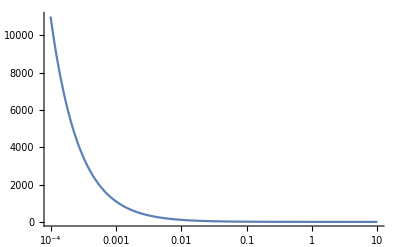

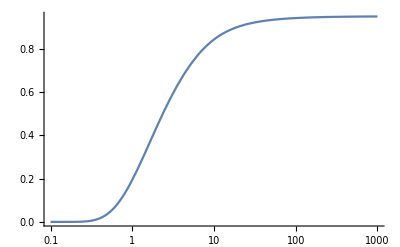

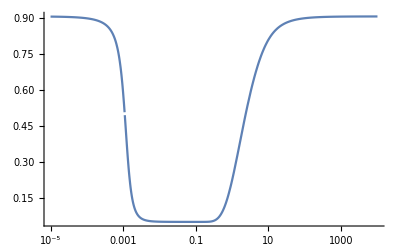

```mathematica
delta= 3*10^-23;                                                              (*(GeV)^2*)                                       
rh[r_]:=160*4.36*10^-18*Exp[-r];                   (*(GeV)^4*)                                                                
theta= ArcSin[Sqrt[0.05]]   ;                                                                                                    
Cos[2*theta]                                   ;                                                                                                    
F=1-Tan[theta]^2                        ;  
Ac[En_]:=2*Sqrt[2]*1.166*10^-5*1/0.938*rh[0]*En;                                                                     


Ac[x]                                                                                                                                                                                                                                (*ANS------1*)

thetam[En_]:=0.5* ArcTan[(delta*Sin[2 *theta])/(-Ac[En]+delta*Cos[2 *theta])];                               
LogLinearPlot[Sin[2*thetam[En]]^2,{En,10^-6,1}, PlotRange->Full]                                                                                                            (*thetam-----Plot------1*)

Costhetam[En_]:=Abs[(Ac[En]-delta*Cos[2*theta])]/((Ac[En]-delta*Cos[2*theta])^2+(delta*Sin[2*theta])^2)^0.5;
thetam[x]                                                                                                                                                                           ;                                                                             
Simplify@Solve[FullSimplify[Ac[En]-delta*Cos[2*theta]]==0,{En}]                                                                                    (*ANS------2*)
Ea=0.001100820697938                                                                                                                                                                                              (*ANS------3*)



gamma[En_]:= delta*Sin[2*theta]^2/(2*En*Cos[2*theta]*1/(5*10^13)*10/(6.96*10^10));                              
gamma[x]                                                                                                                                                                                                                             (*ANS------4*)
LogLinearPlot[gamma[En],{En,10^-4,10},PlotRange->Full]                                                                                                                                          (*Gamma plot-----2*)

pc[En_]:= (E^(-Pi/2*gamma[En]*F)-E^(-Pi/2*gamma[En]*F/Sin[theta]^2))/(1-E^(-Pi/2*gamma[En]*F/Sin[theta]^2))*HeavisideTheta[Ac[En]-delta*Cos[2*theta]];
LogLinearPlot[pc[En],{En,10^-1,1000}]                                                                                                                                                                                                                                                 (*PC plot-----3*)

Pm[En_]:=(0.5 + (0.5-pc[En])*Cos[2*theta]*Cos[2*thetam[En]])*HeavisideTheta[Ea-En]+(0.5 + (0.5-pc[En])*Cos[2*theta]*-1*Cos[2*thetam[En]])*HeavisideTheta[En-Ea]
LogLinearPlot[Pm[En],{En,10^-5,10000}, PlotRange->Full]                                                                                                                                       (*P(v->v)---plot-----4*)
```

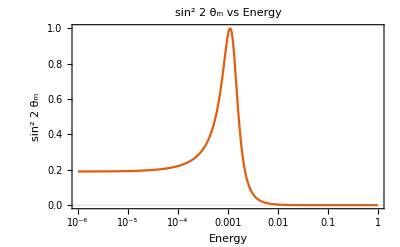

```mathematica
Show[%66,FrameLabel->{{HoldForm[sin^2 2 Subscript[θ, m]],None},{HoldForm[Energy],None}},PlotLabel->HoldForm[sin^2 2 Subscript[θ, m] vs Energy],LabelStyle->{GrayLevel[0]}]
```

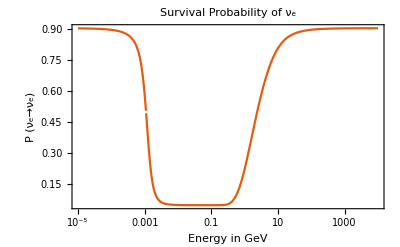

```mathematica
Show[%36,FrameLabel->{{HoldForm[HoldForm[P (Subscript[ν, e]->Subscript[ν, e])]],None},{HoldForm[Energy in GeV],None}},PlotLabel->HoldForm[Survival Probability of Subscript[ν, e]],LabelStyle->{GrayLevel[0]}]
```